```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=320; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
(*1.43 magic number*)
snu=(snu1+snu2);
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
(*slice=snu*n/(bin/2);
xevent=ConstantArray[0,bin+1];
pevent=ConstantArray[0,bin+1];
(*63*)
(*X-Quadrature of the Data*)
xsize=Dimensions[allData[[6]][[19;;]]];
xsize=xsize[[1]];
xquad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,xsize}];

(*P-Quadrature of the Data*)
psize=Dimensions[allData[[3]][[19;;]]];
psize=psize[[1]];
pquad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,psize}];*)
```

## Squeezed vacuum generation

```mathematica
slice=snu*n/(bin/2);
(*hbar=1*)
(*squeezing parameter *)
r=0.5;
(*Rotation parameter θ*)
ang=Pi/4;

funcx=Integrate[1/Pi*Exp[-((x*Cos[ang]-p*Sin[ang])^2)/Exp[-1]-
((x*Sin[ang]+p*Cos[ang])^2)/Exp[1]],{p,-Infinity,Infinity}];
plusx[x_]=funcx;

funcp=
Integrate[1/Pi*Exp[-((x*Cos[ang]-p*Sin[ang])^2)/Exp[-1]-
((x*Sin[ang]+p*Cos[ang])^2)/Exp[1]],{x,-Infinity,Infinity}];
plusp[p_]=funcp;
```

## Squeezed vacuum Event

```mathematica
xevent=Table[(plusx[(i-bin/2)/(bin/2)*n]),{i,0,bin}];
xnorm=Sum[xevent[[i]],{i,1,bin+1}];
xnorm//N
xevent=xevent/xnorm;
pevent=Table[(plusp[(i-bin/2)/(bin/2)*n]),{i,0,bin}];
pnorm=Sum[pevent[[i]],{i,1,bin+1}];
pnorm//N
pevent=pevent/pnorm;
```

20.

20.

## Counting Events

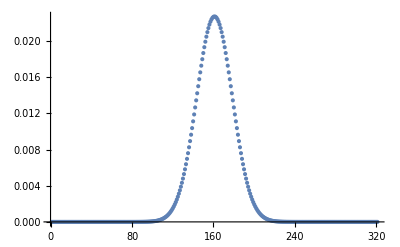

-Graphics-

```mathematica
(*(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
xevent=xevent/xsize;
pevent=pevent/psize;*)

(*Gmn is imported, discretized and normalized occurence of event*)
G={xevent,pevent}//N;
ListPlot[xevent, PlotRange->Full]
ListPlot[pevent,PlotRange->Full]
```

## Normalization Parameter for Projector

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
```

20.

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/2};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,2}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
solution=FindMinimum[Q,kernel];

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(0.811617 | 0.0170141+0.00339925 ⅈ | 0.000866498-0.0852871 ⅈ | 0.0161563-0.00206941 ⅈ | -0.0267023+0.00887219 ⅈ | -0.000826846-0.00324174 ⅈ | -0.00182023+0.00571802 ⅈ | -0.000385537-0.000287469 ⅈ | -0.000542744+0.000258518 ⅈ
0.0170141-0.00339925 ⅈ | 0.122868 | -0.00329492-0.00328145 ⅈ | -0.00142558+0.00334896 ⅈ | 0.00960322-0.00135963 ⅈ | -0.00202374+0.000675633 ⅈ | 0.00204192+0.000698528 ⅈ | 0.000588337-0.000716278 ⅈ | -0.000166343+0.000282168 ⅈ
0.000866498+0.0852871 ⅈ | -0.00329492+0.00328145 ⅈ | 0.0535085 | -0.00395014+0.000635749 ⅈ | 0.00100699-0.0114771 ⅈ | 0.00175558+0.00026668 ⅈ | -0.00274047-0.00181753 ⅈ | 0.000127186+0.00031114 ⅈ | -1.56834×10^-6-0.000386185 ⅈ
0.0161563+0.00206941 ⅈ | -0.00142558-0.00334896 ⅈ | -0.00395014-0.000635749 ⅈ | 0.00570223 | -0.00244723-0.000227795 ⅈ | -0.000481476+0.0000689519 ⅈ | 0.000518174+0.000541561 ⅈ | -0.000292002-0.000373361 ⅈ | -0.0000357731+0.0001717 ⅈ
-0.0267023-0.00887219 ⅈ | 0.00960322+0.00135963 ⅈ | 0.00100699+0.0114771 ⅈ | -0.00244723+0.000227795 ⅈ | 0.00511505 | -0.0000566574+0.000439959 ⅈ | 0.00038154-0.00078163 ⅈ | 0.000160115-0.0000346279 ⅈ | 0.0000678706-0.0000205608 ⅈ
-0.000826846+0.00324174 ⅈ | -0.00202374-0.000675633 ⅈ | 0.00175558-0.00026668 ⅈ | -0.000481476-0.0000689519 ⅈ | -0.0000566574-0.000439959 ⅈ | 0.000340429 | -0.000219948-0.000342676 ⅈ | -0.0000663015+0.0000748939 ⅈ | 0.000040829-0.0000465705 ⅈ
-0.00182023-0.00571802 ⅈ | 0.00204192-0.000698528 ⅈ | -0.00274047+0.00181753 ⅈ | 0.000518174-0.000541561 ⅈ | 0.00038154+0.00078163 ⅈ | -0.000219948+0.000342676 ⅈ | 0.00067458 | -0.0000571343-0.0000452335 ⅈ | 0.0000276832+0.0000727569 ⅈ
-0.000385537+0.000287469 ⅈ | 0.000588337+0.000716278 ⅈ | 0.000127186-0.00031114 ⅈ | -0.000292002+0.000373361 ⅈ | 0.000160115+0.0000346279 ⅈ | -0.0000663015-0.0000748939 ⅈ | -0.0000571343+0.0000452335 ⅈ | 0.000155726 | -0.0000405206-3.60436×10^-6 ⅈ
-0.000542744-0.000258518 ⅈ | -0.000166343-0.000282168 ⅈ | -1.56834×10^-6+0.000386185 ⅈ | -0.0000357731-0.0001717 ⅈ | 0.0000678706+0.0000205608 ⅈ | 0.000040829+0.0000465705 ⅈ | 0.0000276832-0.0000727569 ⅈ | -0.0000405206+3.60436×10^-6 ⅈ | 0.0000183839)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=n+1;
xrange={-5,5};
yrange={-5,5};
linespace=100;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
Min[list]
disp=Sqrt[((50-pos[[1,1]])/10)^2+((50-pos[[1,2]])/10)^2]//N
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False,DataRange->{{-5,5},{-5,5}}]
```

{{51,51}}

-0.0000772071

0.141421

-Graphics3D-